```mathematica
GetData[fname_] := Module[{f=fname, json, mdata},
json = Import[fname, "RawJSON"];
mdata=json[["metadata"]];
<|"num_crafts"-> mdata[["max_num_crafts"]], "num_samples"-> mdata[["max_num_samples"]], "sim_time" -> mdata[["sim_time"]], "elapsed_time" -> mdata[["time_end"]]-mdata[["time_start"]]|>
]
```

```mathematica
dataFiles = FileNames["*.json",NotebookDirectory[]<>"../experiment_results/",Infinity ];
```

```mathematica
simData = ParallelMap[GetData, dataFiles]; (*GetData/@dataFiles;*)
numDPoint=Length[simData]
```

50

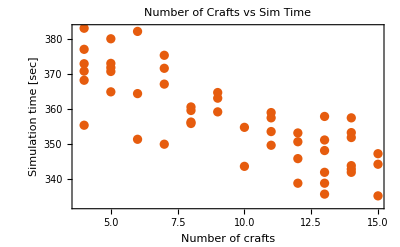

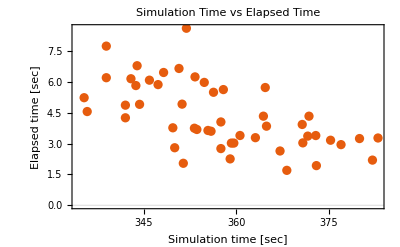

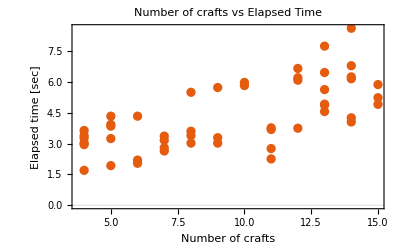

```mathematica
ListLinePlot[
	Values[simData[[All, {"num_crafts", "sim_time"}]]],
	Joined->False,
	PlotLabel->"Number of Crafts vs Sim Time",
	FrameLabel->{"Number of crafts", "Simulation time [sec]"},
	PlotTheme->"Scientific"]
ListLinePlot[
	Values[simData[[All, {"sim_time", "elapsed_time"}]]],
	Joined->False,
	PlotLabel->"Simulation Time vs Elapsed Time",
	FrameLabel->{"Simulation time [sec]", "Elapsed time [sec]"},
	PlotTheme->"Scientific"]
ListLinePlot[
	Values[simData[[All, {"num_crafts", "elapsed_time"}]]],
	Joined->False,
	PlotLabel->"Number of crafts vs Elapsed Time",
	FrameLabel->{"Number of crafts", "Elapsed time [sec]"},
	PlotTheme->"Scientific"]
```